## Importando e manipulando o catálogo

```mathematica
SetDirectory[NotebookDirectory[]];

catalogo= Import["catalogo.csv", "Table"];        (*Importa o catálogo e guarda no formato de uma tabela*)
redshift=catalogo[[2;;,1]];   (*Redshift*)
dL= catalogo[[2;;,2]];                (*Luminosity distance*)
sdL= catalogo[[2;;,3]];              (*Standard deviation da luminosity distance*)(*Sdt = raiz do erro observacional*)
nsn=Length[redshift];               (*Número de supernovas do catálogo*)
```

## Definição das constantes

```mathematica
Clear[Ωm,Ωκ,ΩL,z,zp,H0]
c= 2.998*10^5;                                           (*Velocidade da luz:  Kms^-1*)
DH[H0_]= c/H0;                                       (*Distância de Hubble: 4380 +/- 150 Mpc*)
ΩL[Ωm_,Ωκ_]:= 1- Ωm - Ωκ;           (*Definição do Omega_Lambda em função do Omega de matéria e de curvatura*)
```

## Equações de Distâncias e χ2

### E (z)

```mathematica
Ez[z_,Ωm_,Ωκ_]:=√(Ωm *(1+z)^3+ Ωκ*(1+z)^2+ ΩL[Ωm,Ωκ])
```

### DC - Comoving distance (line-of-sight)

```mathematica
integral1[z_,Ωm_,Ωκ_]:= NIntegrate[1/Ez[zp,Ωm,Ωκ],{zp,0,z},PrecisionGoal->4,AccuracyGoal->Infinity,WorkingPrecision->8]

DC[z_,Ωm_,Ωκ_,H0_]:=DH[H0]*integral1[z,Ωm,Ωκ]
```

### DM - Comoving distance (transverse)

```mathematica
eq1[z_,Ωm_,Ωκ_,H0_]:= DH[H0]* (1/(√Ωκ))*Sinh[√Ωκ*(DC[z,Ωm,Ωκ,H0]/DH[H0])];
eq2[z_,Ωm_,Ωκ_,H0_]:=DH[H0]* (1/(√Norm[Ωκ]))*Sin[√Norm[Ωκ]*(DC[z,Ωm,Ωκ,H0]/DH[H0])];

DM[z_,Ωm_,Ωκ_,H0_]:= Which[Ωκ>0,eq1[z,Ωm,Ωκ,H0],Ωκ<0, eq2[z,Ωm,Ωκ,H0],Ωκ==0,DC[z,Ωm,Ωκ,H0]];
```

### DL - Luminosity distance

```mathematica
DL[z_,Ωm_,Ωκ_,H0_]:= (1+z)*DM[z,Ωm,Ωκ,H0];
```

### χ2

```mathematica
χ2[Ωm_,Ωκ_,H0_]:=Module[{},
nsteps=30;

DLvec=Map[{#,DL[#,Ωm,Ωκ,H0]}&,Range[0,Max[redshift]+1.01 Max[redshift]/nsteps,Max[redshift]/nsteps]];
DLinterp=Interpolation[DLvec];
 Total[Table[(dL[[i]]- DLinterp[redshift[[i]]])^2/(sdL[[i]])^2,{i,1,nsn}]]]
```

## Likelihood

```mathematica
CloseKernels[];
```

```mathematica
LaunchKernels[16];
```

```mathematica
Newlikelihood[Ωm_,Ωκ_,H0_] :=Exp[-1/2 χ2[Ωm,Ωκ,H0]];
```

### Construindo a grid:

```mathematica
{Ωmdim,Ωκdim,H0dim}=50{1,1,1};
{Ωmmin, Ωmmax}= {0,1};
{Ωκmin,Ωκmax}={-1.2,1.2};   
{H0min, H0max}={67,73};          
ΔΩm= (Ωmmax-Ωmmin)/(Ωmdim-1);
ΔΩκ=(Ωκmax-Ωκmin)/(Ωκdim-1);
ΔH0=(H0max-H0min)/(H0dim-1);
Ωmvec=Range[Ωmmin,Ωmmax, ΔΩm];
Ωκvec=Range[Ωκmin,Ωκmax,ΔΩκ];
H0vec=Range[H0min,H0max,ΔH0];
```

## Posterior

```mathematica
zmax=0.7;

NEWposterior1= ParallelTable[If[(Ωmvec[[i]](1+zmax)^3+ Ωκvec[[j]](1+zmax)^2+ ΩL[Ωmvec[[i]],Ωκvec[[j]]])<0,{Ωmvec[[i]],Ωκvec[[j]],H0vec[[k]],10.^-10},
{Ωmvec[[i]],Ωκvec[[j]],H0vec[[k]],Newlikelihood[Ωmvec[[i]],Ωκvec[[j]],H0vec[[k]]]}],  {i,1,Ωmdim},{j,1,Ωκdim},{k,1,H0dim}];

Export["3.0-posterior_grid_50x50x50.list",NEWposterior1,"List"];
```

Se já tiver o arquivo.list, rodar apenas a linha abaixo:

```mathematica
NEWposterior1=ToExpression[Import["3.0-posterior_grid_50x50x50.list","List"]];
```

## Marginalization

```mathematica
Dimensions[post2D=NEWposterior1[[All,All,All,4]]]
```

{50,50,50}

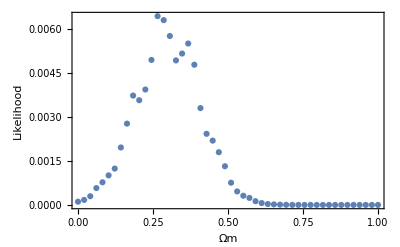

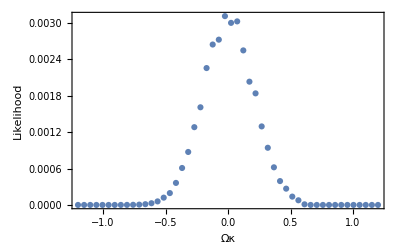

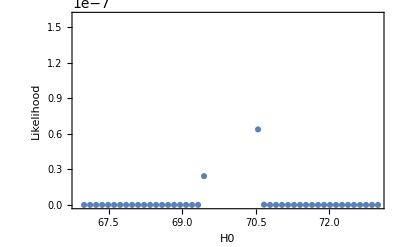

```mathematica
postmargOkh=Thread[{Ωmvec,ΔΩκ ΔH0 Total[post2D,{2,3}]}] ;(*Marginalizando em relação a Ωκ e H0,ou seja, sobra só o Ωm. A primeira entrada é o parâmetro que "sobra", a segunda é uma soma sobre os parâmteros que estou marginalizando (integrando sobre eles)multiplicado pelos deltas para normalizar o resultado*)
ListPlot[postmargOkh,Frame->True,FrameLabel->{"Ωm","Likelihood"}]  (*Gráfico da distribuição para Ωm*)

postmargOmh=Thread[{Ωκvec,ΔΩm ΔH0 Total[Total[post2D,{3}],{1}]}];  (*Análogo ao caso anterior: marginalizção em Ωm e H0 para encontrar a distribuição para Ωκ*)
ListPlot[postmargOmh,Frame->True,FrameLabel->{"Ωκ","Likelihood"}] (*Gráfico da distribuição para Ωκ*)

postmargOmOk=Thread[{H0vec,ΔΩm ΔΩκ  Total[post2D,{1,2}]}]; (*Análogo ao caso anterior: marginalizção em Ωm e Ωκ para encontrar a distribuição para H0*)
ListPlot[postmargOmOk,Frame->True,FrameLabel->{"H0","Likelihood"}] 
(*Gráfico da distribuição para H0*)
```

```mathematica
Best-fit
(*Best-fit para Ωm*)
In[99]:=maxSecondEntry=Max[postmargOkh[[All,2]]];

sublistWithMaxSecond=Select[postmargOkh,#[[2]]==maxSecondEntry&];

firstEntry=sublistWithMaxSecond[[1,1]]//N
Out[101]=0.265306
(*Best-fit para Ωκ*)
In[96]:=maxSecondEntry=Max[postmargOmh[[All,2]]];

sublistWithMaxSecond=Select[postmargOmh,#[[2]]==maxSecondEntry&];

firstEntry=sublistWithMaxSecond[[1,1]]//N
Out[98]=-0.0244898
(*Best-fit para H0*)
In[93]:=maxSecondEntry=Max[postmargOmOk[[All,2]]];

sublistWithMaxSecond=Select[postmargOmOk,#[[2]]==maxSecondEntry&];

firstEntry=sublistWithMaxSecond[[1,1]]//N
Out[95]=70.0612
```

## Contour Plot

```mathematica
post2D//Dimensions  (*Todos os valores da likelihood*)
```

{50,50,50}

Marginalizando um caso por vez:

```mathematica
margOm=ΔΩm Total[post2D,{1}];          (*Marginalização - Equivalente a integral da posterior em relação a dΩm*)
margOk=ΔΩκ Total[post2D,{2}];          (*Marginalização - Equivalente a integral da posterior em relação a dΩκ*)
margH0=ΔH0 Total[post2D,{3}];          (*Marginalização - Equivalente a integral da posterior em relação a dH0*) 


margOm//Dimensions                                    (*Verificação de como a marginzalização diminiu uma dimensão do resultado*)
```

General::munfl: (4.52843×10^-308)/49 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0489796 1.49298×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.92223×10^-308 6)/49 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.29606×10^-307 6)/49 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.22818×10^-307 6)/49 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{50,50}

Gerando as listas no formato {param1, param2, likelihood} para cada caso:

```mathematica
margOm2D=NEWposterior1[[1,All,All,{2,3,4}]];            (*Constrói a lista com Ωκ, H0 e likelihood original*)
margOκ2D=NEWposterior1[[All,1,All,{1,3,4}]];            (*Constrói a lista com Ωm, H0 e likelihood original*)
margHo2D=NEWposterior1[[All,All,1,{1,2,4}]];             (*Constrói a lista com Ωm, Ωκ e likelihood original*)  


Dimensions[margOm2D]      (*Verifica se as dimensão estão corretas*)
```

{50,50,3}

Trocando o valor da likelihood original pela likelihood após a marginalização:

```mathematica
margOm2D[[All,All,3]]=margOm;   
margOκ2D[[All,All,3]]=margOk; 
margHo2D[[All,All,3]]=margH0;
```

Aplicando um Flatten para que eu tenha uma lista única com dim1xdim2 (dimensões da grid) sublistas, cada um com apenas 3 parâmetros.

```mathematica
margOmflat=Flatten[margOm2D,1];   
margOκflat=Flatten[margOκ2D,1]; 
margH0flat=Flatten[margHo2D,1]; 

Dimensions[margOmflat]     (*Testa se as dimensões estão corretas*)
```

{2500,3}

Trocando o valor da likelihood pelo -log like:

```mathematica
margOmflat[[All,3]]=-Log[margOmflat[[All,3]]+10^-300.];  
 margOκflat[[All,3]]=-Log[margOκflat[[All,3]]+10^-300.];  
 margH0flat[[All,3]]=-Log[margH0flat[[All,3]]+10^-300.];
```

Colocando o mínimo do chi quadrado em zero :

```mathematica
margOmflat[[All,3]]-=Min[margOmflat[[All,3]]];   
margOκflat[[All,3]]-=Min[margOκflat[[All,3]]]; 
margH0flat[[All,3]]-=Min[margH0flat[[All,3]]];
```

Calculando o min e max do chi quadrado:

```mathematica
MinMax[margOmflat[[All,3]]]  
MinMax[margOκflat[[All,3]]] 
MinMax[margH0flat[[All,3]]]
```

{0.,686.727}

{0.,687.596}

{0.,688.695}

Valores para as regiões de confiança σ = 0.683, 0.954, 0.997.

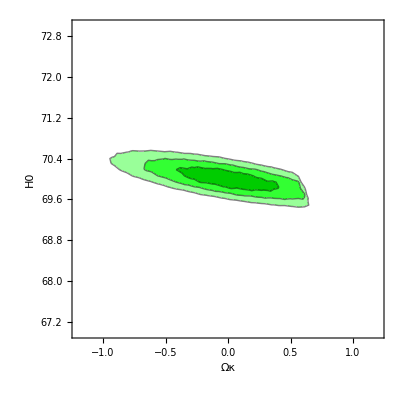

```mathematica
plot1=ListContourPlot[margOmflat,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Green,.2],Lighter[Green,.2],Lighter[Green,.6],White},Frame->True,FrameLabel->{"Ωκ","H0"}]
```

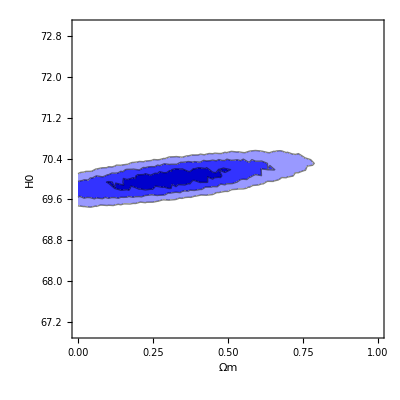

```mathematica
plot2=ListContourPlot[margOκflat,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Blue,.2],Lighter[Blue,.2],Lighter[Blue,.6],White},Frame->True,FrameLabel->{"Ωm","H0"}]
```

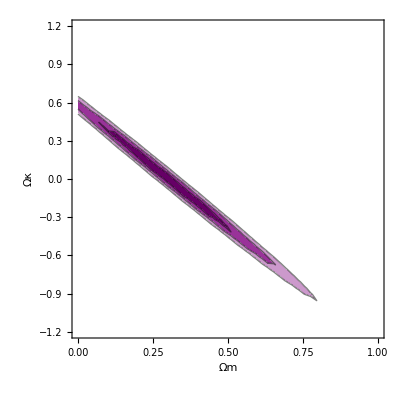

```mathematica
plot3=ListContourPlot[margH0flat,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Purple,.2],Lighter[Purple,.2],Lighter[Purple,.6],White},Frame->True,FrameLabel->{"Ωm","Ωκ"}]
```

```mathematica
Export["3.1-plot_OkxH0.list",margOmflat,"List"];
Export["3.2-plot_OmxH0.list",margOκflat,"List"];
Export["3.3-plot_OmxOk_new.list",margH0flat,"List"];
```